```mathematica
<<Local`SrednickiInit`
```

mχk2+x-x^2==0
→ zeros at: {{x→1/2 (1-√(1+4 mχk2))},{x→1/2 (1+√(1+4 mχk2))}}

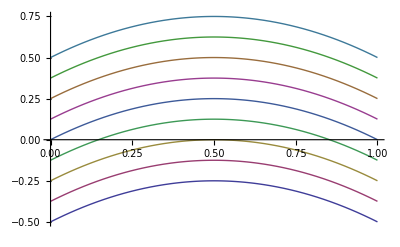

```mathematica
PR[
e2511=x(1-x)k^2+mχ^2==0;
t2511=e2511/.mχ^2->mχk2 k^2//Simplify;
t2511=Map[#/k&,t2511],Yield,
"zeros at: ",
Solve[t2511,{x}]
]
Plot[Evaluate[Table[Tooltip[(t2511/.mχk2->y),Subscript[m, χ]^2/k^2==y],{y,-1/2,1/2,1/8}]],{x,0,1}]
```